# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## VQE on the virtual device: Solve H_3

```mathematica
distances=Range[0.25,5,0.05]
```

{0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:34:27 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:38:34, fev:820, <E>: -0.30494661602510365 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 2, 25, 82}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:39:21, fev:1111, <E>: -0.30494661602510365 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 2, 25, 95}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:40:50, fev:1505, <E>: -0.30494661602510365 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 9, 2, 25, 122}

dist 0.25 done with runtime 6.45499 min ϵ=0.00732329

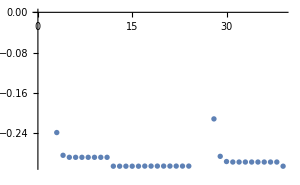

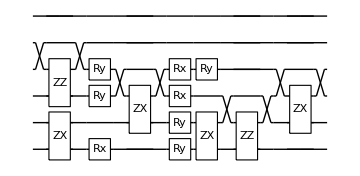

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:40:55 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:44:57, fev:836, <E>: -0.5751783807467554 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 22, 69}

@cycle2:Wed 15 Feb 2023 21:45:46, fev:1240, <E>: -0.5930973349061224 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 33, 79}

@cycle3:Wed 15 Feb 2023 21:46:08, fev:1532, <E>: -0.5938173418919194 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 36, 93}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:46:32, fev:1802, <E>: -0.5938173418919194 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 36, 102}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 21:47:26, fev:2194, <E>: -0.5938173418919194 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 36, 123}

dist 0.3 done with runtime 6.52563 min ϵ=0.00798637

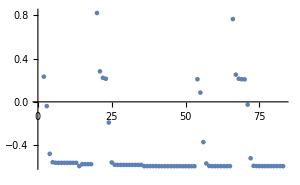

-Graphics-

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:47:26 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:52:42, fev:1137, <E>: -0.7803166608766541 nansatz: 28 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 20, 76}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:53:37, fev:1402, <E>: -0.7803166608766541 nansatz: 28 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 20, 82}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:55:29, fev:1795, <E>: -0.7803166608766541 nansatz: 28 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 20, 96}

dist 0.35 done with runtime 8.44937 min ϵ=0.00895273

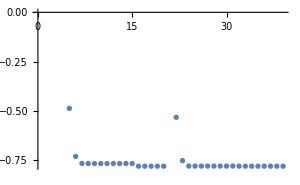

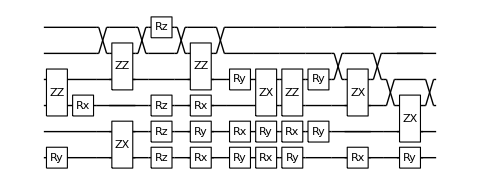

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:55:53 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:00:32, fev:862, <E>: -0.9042642447903941 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 22, 98}

@cycle2:Wed 15 Feb 2023 22:00:55, fev:1172, <E>: -0.9042642524623643 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 22, 103}

@cycle3:Wed 15 Feb 2023 22:01:13, fev:1478, <E>: -0.9042642567767734 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 26, 110}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:01:31, fev:1706, <E>: -0.9042642567767734 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 26, 114}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:02:08, fev:2046, <E>: -0.9042642567767734 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 26, 126}

dist 0.4 done with runtime 6.26818 min ϵ=0.00988545

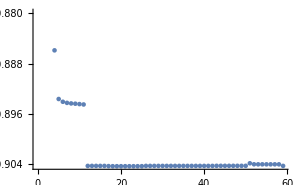

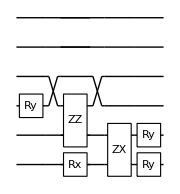

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:02:09 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:06:41, fev:821, <E>: -0.9755827097731975 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 20, 0, 12, 89}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:07:23, fev:1101, <E>: -0.9755827097731975 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 20, 0, 12, 91}

@cycle3:Wed 15 Feb 2023 22:08:37, fev:1612, <E>: -0.9875049801657863 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 29, 0, 24, 100}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:09:02, fev:1932, <E>: -0.9875049801657863 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 29, 0, 24, 114}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:10:05, fev:2346, <E>: -0.9875049801657863 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 29, 0, 24, 152}

dist 0.45 done with runtime 7.92258 min ϵ=0.0109106

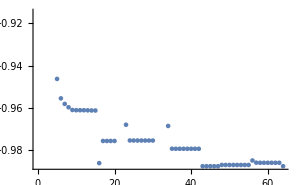

-Graphics-

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:10:05 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:15:54, fev:1247, <E>: -1.0364973879332136 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 20, 63}

@cycle2:Wed 15 Feb 2023 22:17:01, fev:1725, <E>: -1.0425903197613964 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 31, 74}

@cycle3:Wed 15 Feb 2023 22:17:27, fev:2093, <E>: -1.042918487471251 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 17, 3, 32, 79}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:17:47, fev:2342, <E>: -1.042918487471251 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 17, 3, 32, 88}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:18:20, fev:2670, <E>: -1.042918487471251 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 17, 3, 32, 98}

dist 0.5 done with runtime 8.30642 min ϵ=0.0122413

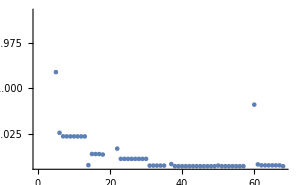

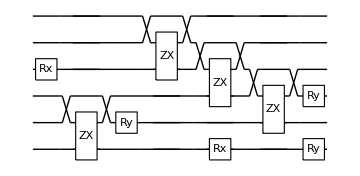

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:18:23 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:23:50, fev:1190, <E>: -1.078385639421841 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 28, 73}

@cycle2:Wed 15 Feb 2023 22:24:45, fev:1633, <E>: -1.0789229914852225 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 31, 83}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:25:17, fev:1871, <E>: -1.0789229914852225 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 31, 91}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:26:09, fev:2211, <E>: -1.0789229914852225 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 31, 100}

dist 0.55 done with runtime 7.98967 min ϵ=0.0137069

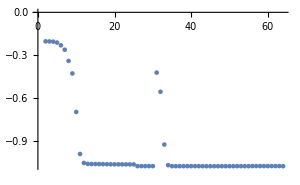

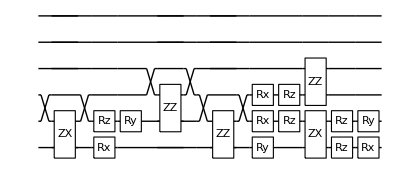

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:26:23 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:31:31, fev:1001, <E>: -1.1000745272592467 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 97}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:32:38, fev:1251, <E>: -1.1000745272592467 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 105}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:34:13, fev:1596, <E>: -1.1000745272592467 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 109}

dist 0.6 done with runtime 8.6535 min ϵ=0.0162115

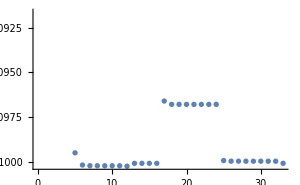

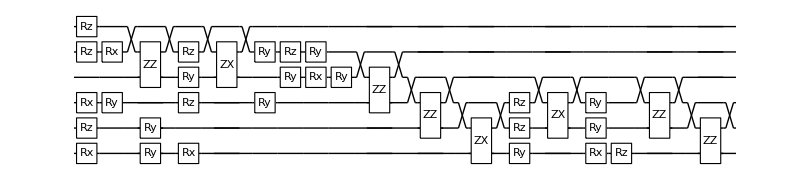

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:35:02 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:39:54, fev:1020, <E>: -1.1123766133427613 nansatz: 22 merged-smallθ-metric-bf-gmerged: {3, 11, 0, 16, 87}

@cycle2:Wed 15 Feb 2023 22:41:07, fev:1490, <E>: -1.11237661337044 nansatz: 22 merged-smallθ-metric-bf-gmerged: {3, 11, 0, 22, 87}

@cycle3:Wed 15 Feb 2023 22:42:30, fev:2006, <E>: -1.1124066205253953 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 11, 0, 25, 95}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:43:23, fev:2261, <E>: -1.1124066205253953 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 11, 0, 25, 104}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:44:30, fev:2582, <E>: -1.1124066205253953 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 11, 0, 25, 113}

dist 0.65 done with runtime 9.85937 min ϵ=0.0174982

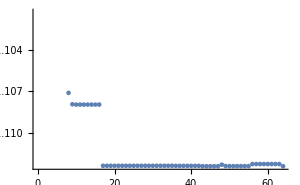

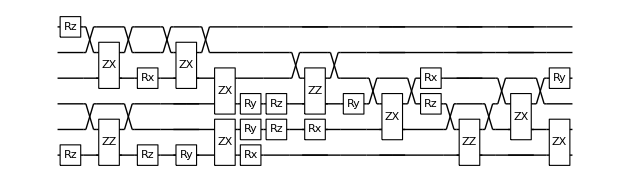

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:44:54 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:49:42, fev:891, <E>: -1.117064626739126 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 23, 83}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:50:08, fev:1139, <E>: -1.117064626739126 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 23, 88}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:50:45, fev:1448, <E>: -1.117064626739126 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 23, 95}

dist 0.7 done with runtime 6.03635 min ϵ=0.0191248

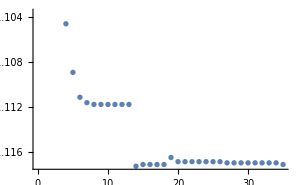

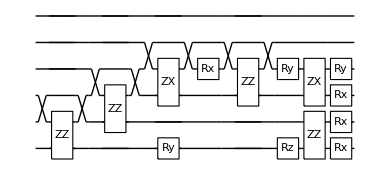

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:50:56 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:55:20, fev:1118, <E>: -1.1161514433793889 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 33, 89}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:55:46, fev:1359, <E>: -1.1161514433793889 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 33, 95}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:56:20, fev:1681, <E>: -1.1161514433793889 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 33, 99}

dist 0.75 done with runtime 5.47399 min ϵ=0.0209656

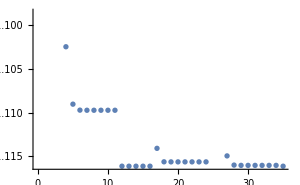

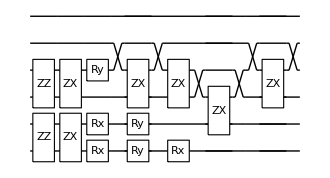

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:56:24 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:00:34, fev:724, <E>: -1.1044379990434512 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 16, 66}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:01:02, fev:952, <E>: -1.1044379990434512 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 16, 70}

@cycle3:Wed 15 Feb 2023 23:01:45, fev:1398, <E>: -1.110689467946488 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 24, 78}

@cycle4:Wed 15 Feb 2023 23:02:16, fev:1782, <E>: -1.1106894851596363 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 27, 92}

@cycle5:Wed 15 Feb 2023 23:02:46, fev:2160, <E>: -1.1108218308457727 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 29, 99}

@cycle6:Wed 15 Feb 2023 23:03:18, fev:2521, <E>: -1.1108481475781742 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 29, 107}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 23:03:46, fev:2827, <E>: -1.1108481475781742 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 29, 114}

I'm slowing down @cycle 8

@cycle8:Wed 15 Feb 2023 23:04:20, fev:3218, <E>: -1.1108481475781742 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 29, 126}

dist 0.8 done with runtime 7.98553 min ϵ=0.0232995

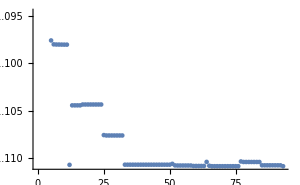

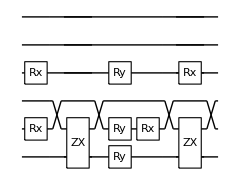

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:04:24 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:09:40, fev:1167, <E>: -1.1021714900062358 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 27, 94}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:10:17, fev:1425, <E>: -1.1021714900062358 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 27, 103}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:11:05, fev:1748, <E>: -1.1021714900062358 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 27, 110}

dist 0.85 done with runtime 6.88948 min ϵ=0.0261904

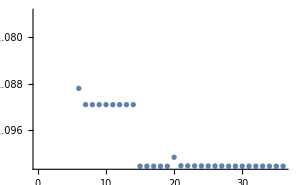

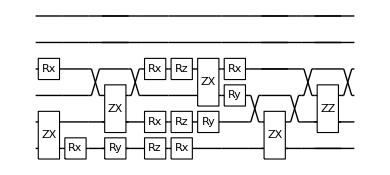

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:11:17 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:16:08, fev:1180, <E>: -1.0845435390618294 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 18, 77}

@cycle2:Wed 15 Feb 2023 23:17:15, fev:1618, <E>: -1.0916256144701635 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 22, 0, 20, 83}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:17:41, fev:1862, <E>: -1.0916256144701635 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 22, 0, 20, 87}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:18:13, fev:2174, <E>: -1.0916256144701635 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 22, 0, 20, 92}

dist 0.9 done with runtime 7.00661 min ϵ=0.0289347

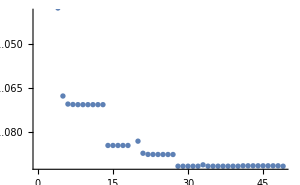

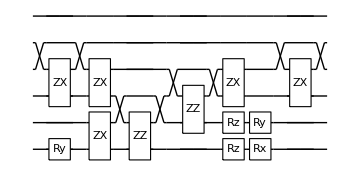

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:18:18 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:22:33, fev:929, <E>: -1.0794329605625534 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 26, 87}

@cycle2:Wed 15 Feb 2023 23:23:24, fev:1408, <E>: -1.079451968894429 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 31, 99}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:23:57, fev:1668, <E>: -1.079451968894429 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 31, 104}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:24:31, fev:1960, <E>: -1.079451968894429 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 31, 110}

dist 0.95 done with runtime 6.42942 min ϵ=0.0318874

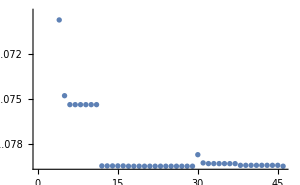

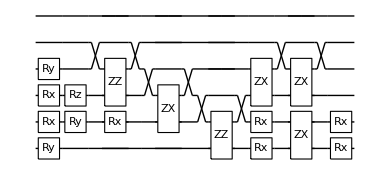

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:24:43 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:30:37, fev:1187, <E>: -1.0652873237745382 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 10, 93}

@cycle2:Wed 15 Feb 2023 23:32:47, fev:1920, <E>: -1.0659025966285414 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 13, 4, 28, 101}

@cycle3:Wed 15 Feb 2023 23:33:08, fev:2229, <E>: -1.0659191833889854 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 13, 4, 32, 108}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:33:28, fev:2471, <E>: -1.0659191833889854 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 13, 4, 32, 113}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 23:33:55, fev:2778, <E>: -1.0659191833889854 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 13, 4, 32, 120}

dist 1. done with runtime 9.21893 min ϵ=0.0352311

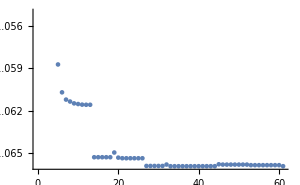

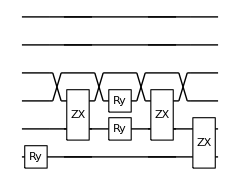

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:33:57 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:38:38, fev:931, <E>: -1.0364918924049233 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 2, 2, 31, 85}

@cycle2:Wed 15 Feb 2023 23:39:13, fev:1249, <E>: -1.0365218264534177 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 2, 2, 31, 94}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:39:46, fev:1515, <E>: -1.0365218264534177 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 2, 2, 31, 100}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:40:25, fev:1822, <E>: -1.0365218264534177 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 2, 2, 31, 104}

dist 1.05 done with runtime 6.61133 min ϵ=0.0426711

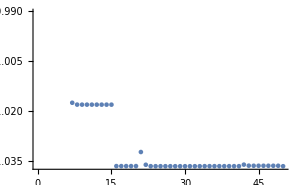

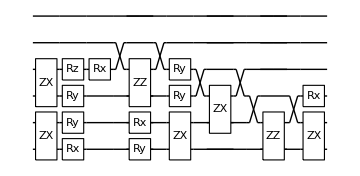

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:40:33 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:44:15, fev:641, <E>: -1.0362890108901732 nansatz: 13 merged-smallθ-metric-bf-gmerged: {5, 2, 4, 9, 81}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:44:44, fev:896, <E>: -1.0362890108901732 nansatz: 13 merged-smallθ-metric-bf-gmerged: {5, 2, 4, 9, 92}

@cycle3:Wed 15 Feb 2023 23:45:34, fev:1390, <E>: -1.0362900337697765 nansatz: 17 merged-smallθ-metric-bf-gmerged: {5, 2, 4, 11, 97}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:46:13, fev:1699, <E>: -1.0362900337697765 nansatz: 17 merged-smallθ-metric-bf-gmerged: {5, 2, 4, 11, 109}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 23:47:15, fev:2116, <E>: -1.0362900337697765 nansatz: 17 merged-smallθ-metric-bf-gmerged: {5, 2, 4, 11, 117}

dist 1.1 done with runtime 6.93217 min ϵ=0.0429029

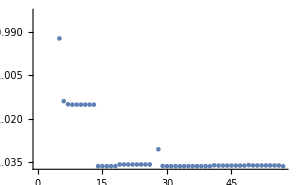

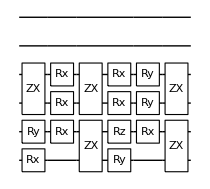

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:47:29 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:51:29, fev:766, <E>: -1.0047451590563607 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 9, 71}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:52:04, fev:1028, <E>: -1.0047451590563607 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 9, 75}

@cycle3:Wed 15 Feb 2023 23:53:01, fev:1537, <E>: -1.0047680129248597 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 81}

@cycle4:Wed 15 Feb 2023 23:54:08, fev:2093, <E>: -1.0047828394355869 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 13, 93}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 23:55:08, fev:2470, <E>: -1.0047828394355869 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 13, 103}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 23:56:04, fev:2854, <E>: -1.0047828394355869 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 13, 111}

dist 1.15 done with runtime 8.83462 min ϵ=0.0519579

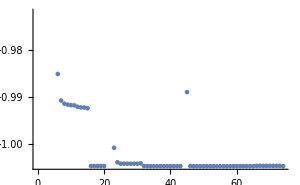

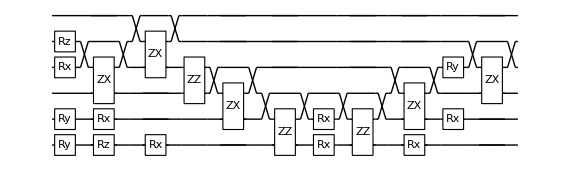

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:56:19 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:00:25, fev:871, <E>: -0.9910022300613675 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 14, 4, 6, 65}

@cycle2:Thu 16 Feb 2023 00:01:18, fev:1368, <E>: -1.0046724645166834 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 19, 69}

@cycle3:Thu 16 Feb 2023 00:01:53, fev:1757, <E>: -1.0048099055081927 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 20, 71}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:02:27, fev:2007, <E>: -1.0048099055081927 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 20, 77}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 00:03:02, fev:2303, <E>: -1.0048099055081927 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 20, 82}

dist 1.2 done with runtime 6.81387 min ϵ=0.0519308

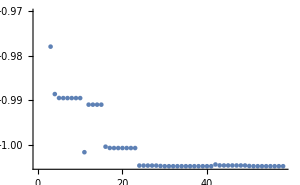

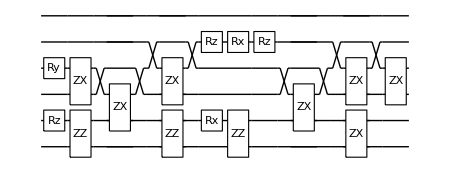

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:03:08 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:07:00, fev:805, <E>: -0.972389292603097 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 8, 88}

@cycle2:Thu 16 Feb 2023 00:08:06, fev:1283, <E>: -0.9723965482141382 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 91}

@cycle3:Thu 16 Feb 2023 00:09:14, fev:1743, <E>: -0.9726088941540373 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 1, 11, 102}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:09:54, fev:2009, <E>: -0.9726088941540373 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 1, 11, 105}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 00:10:37, fev:2319, <E>: -0.9726088941540373 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 18, 1, 11, 109}

dist 1.25 done with runtime 7.73382 min ϵ=0.0625774

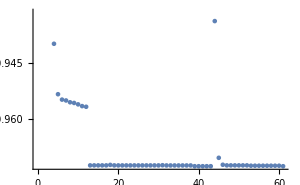

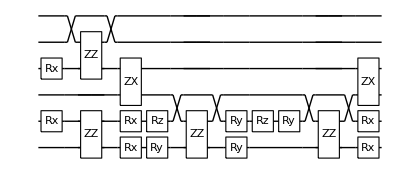

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:10:52 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:15:01, fev:854, <E>: -0.9665815151060587 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 20, 69}

@cycle2:Thu 16 Feb 2023 00:16:03, fev:1275, <E>: -0.9725417287339126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 22, 78}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:16:48, fev:1527, <E>: -0.9725417287339126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 22, 84}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:17:35, fev:1832, <E>: -0.9725417287339126 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 22, 90}

dist 1.3 done with runtime 6.96897 min ϵ=0.0626445

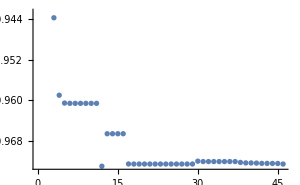

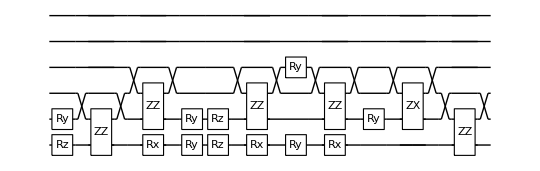

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:17:51 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:21:34, fev:793, <E>: -0.9412056847370425 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 10, 82}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:22:04, fev:1051, <E>: -0.9412056847370425 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 10, 83}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:22:34, fev:1366, <E>: -0.9412056847370425 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 10, 84}

dist 1.35 done with runtime 4.80077 min ϵ=0.0742626

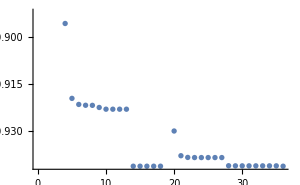

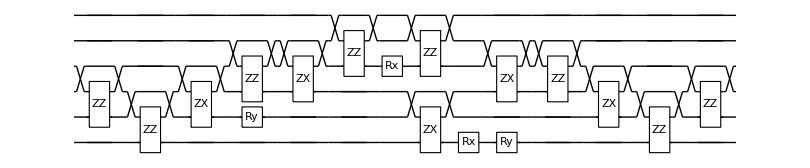

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:22:39 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:28:06, fev:911, <E>: -0.9276504958815373 nansatz: 52 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 0, 65}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:29:29, fev:1147, <E>: -0.9276504958815373 nansatz: 52 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 0, 72}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:31:23, fev:1462, <E>: -0.9276504958815373 nansatz: 52 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 0, 78}

dist 1.4 done with runtime 12.0165 min ϵ=0.0788218

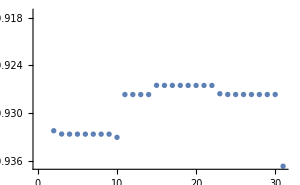

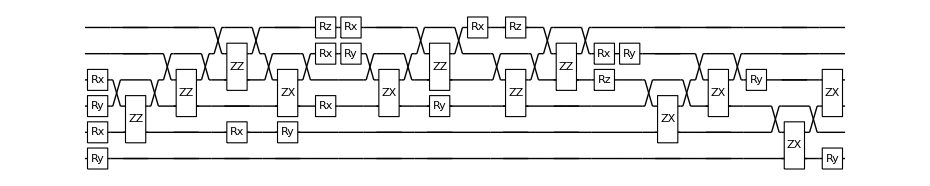

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:34:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:39:02, fev:928, <E>: -0.9106809220866693 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 19, 91}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:39:39, fev:1174, <E>: -0.9106809220866693 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 19, 97}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:40:25, fev:1488, <E>: -0.9106809220866693 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 19, 101}

dist 1.45 done with runtime 5.96059 min ϵ=0.0874684

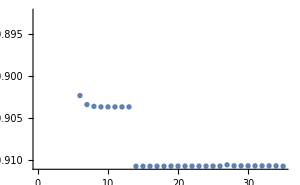

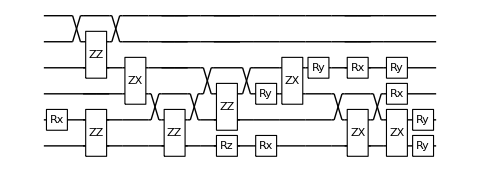

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:40:38 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:45:03, fev:958, <E>: -0.910851475112855 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 3, 28, 79}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:45:34, fev:1246, <E>: -0.910851475112855 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 3, 28, 84}

@cycle3:Thu 16 Feb 2023 00:46:15, fev:1684, <E>: -0.9108514788566072 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 3, 32, 94}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:46:46, fev:1993, <E>: -0.9108514788566072 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 3, 32, 102}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 00:47:27, fev:2393, <E>: -0.9108514788566072 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 12, 3, 32, 112}

dist 1.5 done with runtime 6.9296 min ϵ=0.0872979

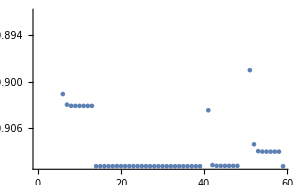

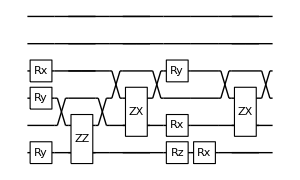

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:47:33 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:51:38, fev:764, <E>: -0.9012904987602546 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 7, 3, 9, 92}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:52:21, fev:1029, <E>: -0.9012904987602546 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 7, 3, 9, 100}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:53:04, fev:1321, <E>: -0.9012904987602546 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 7, 3, 9, 111}

dist 1.55 done with runtime 5.75394 min ϵ=0.0821822

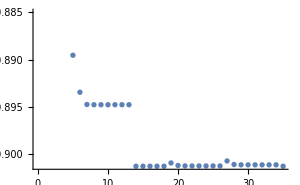

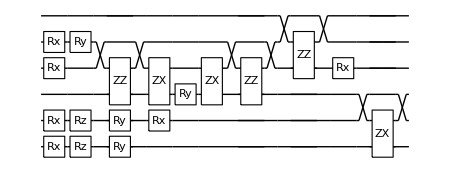

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:53:19 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:56:52, fev:785, <E>: -0.9018932819175951 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 6, 5, 17, 74}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:57:20, fev:1017, <E>: -0.9018932819175951 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 6, 5, 17, 82}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:58:00, fev:1338, <E>: -0.9018932819175951 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 6, 5, 17, 97}

dist 1.6 done with runtime 4.81672 min ϵ=0.0815794

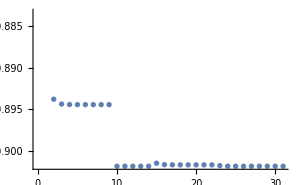

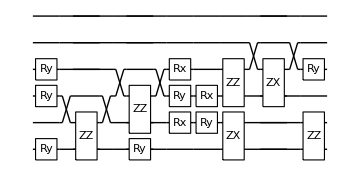

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:58:08 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:01:40, fev:765, <E>: -0.9102294918136211 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 24, 66}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:02:07, fev:1028, <E>: -0.9102294918136211 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 24, 71}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:02:33, fev:1320, <E>: -0.9102294918136211 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 12, 1, 24, 76}

dist 1.65 done with runtime 4.46616 min ϵ=0.0611972

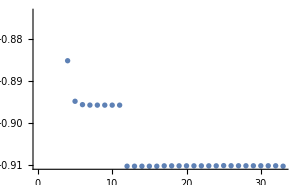

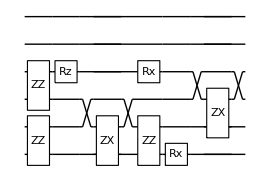

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:02:36 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:06:54, fev:841, <E>: -0.9084850534290979 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 9, 94}

@cycle2:Thu 16 Feb 2023 01:07:36, fev:1261, <E>: -0.9103301474789184 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 27, 102}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:07:48, fev:1489, <E>: -0.9103301474789184 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 27, 109}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 01:08:06, fev:1798, <E>: -0.9103301474789184 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 27, 116}

dist 1.7 done with runtime 5.4992 min ϵ=0.0610965

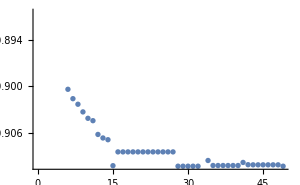

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:08:06 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:12:59, fev:1134, <E>: -0.9162871046569505 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 20, 63}

@cycle2:Thu 16 Feb 2023 01:13:41, fev:1477, <E>: -0.9162886770920371 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 20, 75}

@cycle3:Thu 16 Feb 2023 01:14:38, fev:1941, <E>: -0.9162931731535273 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 22, 86}

@cycle4:Thu 16 Feb 2023 01:15:37, fev:2417, <E>: -0.9162932145403692 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 23, 95}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 01:16:10, fev:2645, <E>: -0.9162932145403692 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 23, 105}

@cycle6:Thu 16 Feb 2023 01:17:32, fev:3272, <E>: -0.9164086536662177 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 26, 118}

@cycle7:Thu 16 Feb 2023 01:18:49, fev:3910, <E>: -0.9165454661300386 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 28, 126}

I'm slowing down @cycle 8

@cycle8:Thu 16 Feb 2023 01:19:35, fev:4219, <E>: -0.9165454661300386 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 28, 136}

I'm slowing down @cycle 9

@cycle9:Thu 16 Feb 2023 01:20:38, fev:4622, <E>: -0.9165454661300386 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 28, 145}

dist 1.75 done with runtime 12.8107 min ϵ=0.0452715

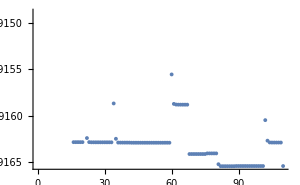

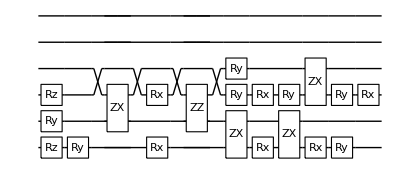

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:20:55 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:25:13, fev:859, <E>: -0.9163523066806616 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 9, 84}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:26:00, fev:1107, <E>: -0.9163523066806616 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 9, 95}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:27:10, fev:1454, <E>: -0.9163523066806616 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 9, 102}

dist 1.8 done with runtime 6.73521 min ϵ=0.0454646

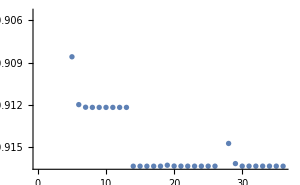

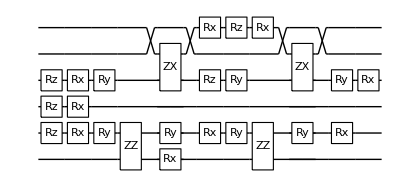

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:27:39 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:32:58, fev:1140, <E>: -0.9153541821936801 nansatz: 30 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 14, 85}

@cycle2:Thu 16 Feb 2023 01:34:38, fev:1794, <E>: -0.9182827801675886 nansatz: 18 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 27, 93}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:35:09, fev:2026, <E>: -0.9182827801675886 nansatz: 18 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 27, 95}

@cycle4:Thu 16 Feb 2023 01:36:04, fev:2518, <E>: -0.9205782281263308 nansatz: 17 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 31, 98}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 01:36:51, fev:2840, <E>: -0.9205782281263308 nansatz: 17 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 31, 99}

@cycle6:Thu 16 Feb 2023 01:38:02, fev:3462, <E>: -0.9206973664941444 nansatz: 18 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 33, 105}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 01:38:54, fev:3866, <E>: -0.9206973664941444 nansatz: 18 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 33, 110}

I'm slowing down @cycle 8

@cycle8:Thu 16 Feb 2023 01:39:50, fev:4314, <E>: -0.9206973664941444 nansatz: 18 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 33, 116}

dist 1.85 done with runtime 12.3493 min ϵ=0.0336415

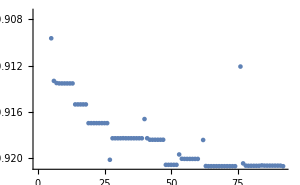

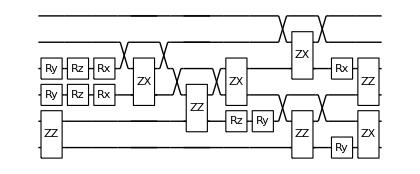

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:40:00 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:44:23, fev:949, <E>: -0.9209054272340444 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 11, 86}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:45:07, fev:1207, <E>: -0.9209054272340444 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 11, 91}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:46:01, fev:1533, <E>: -0.9209054272340444 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 11, 94}

dist 1.9 done with runtime 6.51177 min ϵ=0.0334334

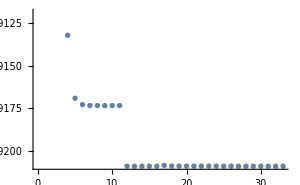

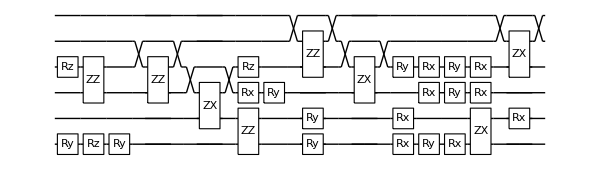

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:46:31 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:49:40, fev:617, <E>: -0.9203555233131373 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 6, 0, 21, 83}

@cycle2:Thu 16 Feb 2023 01:50:07, fev:978, <E>: -0.9223786276797774 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 9, 1, 25, 95}

@cycle3:Thu 16 Feb 2023 01:50:29, fev:1314, <E>: -0.9225543784135503 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 12, 1, 25, 98}

@cycle4:Thu 16 Feb 2023 01:50:53, fev:1709, <E>: -0.9241125580380548 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 1, 26, 102}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 01:51:14, fev:1950, <E>: -0.9241125580380548 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 1, 26, 108}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 01:51:35, fev:2248, <E>: -0.9241125580380548 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 12, 1, 26, 113}

dist 1.95 done with runtime 5.1375 min ϵ=0.0245286

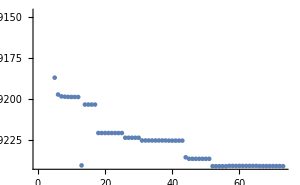

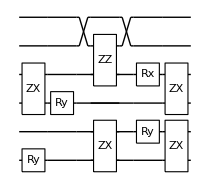

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:51:39 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:55:32, fev:783, <E>: -0.9245329978984448 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 30, 77}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:55:54, fev:1039, <E>: -0.9245329978984448 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 30, 81}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:56:17, fev:1348, <E>: -0.9245329978984448 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 30, 88}

dist 2. done with runtime 4.69672 min ϵ=0.0241081

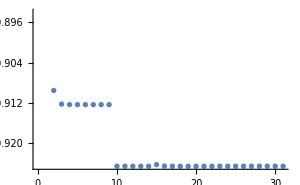

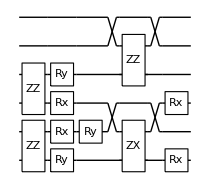

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:56:21 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:00:17, fev:827, <E>: -0.9266748468904928 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 11, 73}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 02:00:43, fev:1068, <E>: -0.9266748468904928 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 11, 78}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 02:01:18, fev:1388, <E>: -0.9266748468904928 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 11, 82}

dist 2.05 done with runtime 5.06014 min ϵ=0.0176998

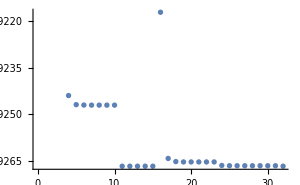

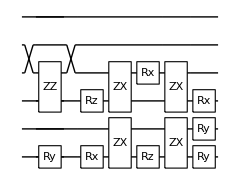

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:01:24 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:04:53, fev:693, <E>: -0.9269351282505085 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 6, 89}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 02:05:23, fev:928, <E>: -0.9269351282505085 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 6, 94}

@cycle3:Thu 16 Feb 2023 02:06:23, fev:1445, <E>: -0.9269351536028196 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 9, 99}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:07:03, fev:1740, <E>: -0.9269351536028196 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 9, 105}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:08:04, fev:2159, <E>: -0.9269351536028196 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 9, 112}

dist 2.1 done with runtime 6.86236 min ϵ=0.0174395

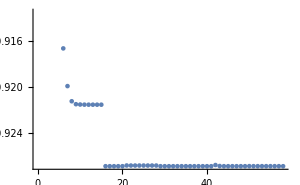

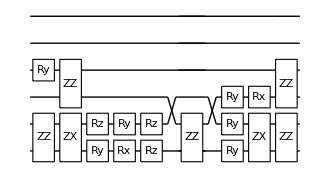

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:08:16 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:12:19, fev:725, <E>: -0.9285146917406971 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 22, 88}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 02:12:39, fev:967, <E>: -0.9285146917406971 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 22, 92}

@cycle3:Thu 16 Feb 2023 02:13:07, fev:1382, <E>: -0.9286722163754395 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 28, 101}

@cycle4:Thu 16 Feb 2023 02:13:35, fev:1780, <E>: -0.9286788170704617 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 29, 115}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:13:59, fev:2091, <E>: -0.9286788170704617 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 29, 127}

@cycle6:Thu 16 Feb 2023 02:14:33, fev:2520, <E>: -0.9286801574941056 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 29, 135}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 02:15:01, fev:2884, <E>: -0.9286801574941056 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 29, 143}

@cycle8:Thu 16 Feb 2023 02:15:37, fev:3389, <E>: -0.9286801594073875 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 29, 152}

@cycle9:Thu 16 Feb 2023 02:16:20, fev:3941, <E>: -0.9286814857180825 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 32, 162}

@cycle10:Thu 16 Feb 2023 02:17:02, fev:4535, <E>: -0.9287611203773797 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 177}

I'm slowing down @cycle 11

@cycle11:Thu 16 Feb 2023 02:17:46, fev:5005, <E>: -0.9287611203773797 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 183}

I'm slowing down @cycle 12

@cycle12:Thu 16 Feb 2023 02:18:41, fev:5562, <E>: -0.9287611203773797 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 194}

dist 2.15 done with runtime 10.5195 min ϵ=0.0124629

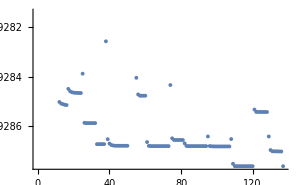

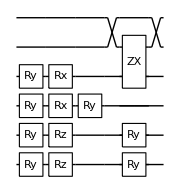

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:18:48 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:22:48, fev:792, <E>: -0.9285082438092119 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 5, 3, 35, 81}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 02:23:06, fev:1031, <E>: -0.9285082438092119 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 5, 3, 35, 83}

@cycle3:Thu 16 Feb 2023 02:23:32, fev:1429, <E>: -0.928751922238648 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 10, 3, 36, 95}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:23:54, fev:1742, <E>: -0.928751922238648 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 10, 3, 36, 102}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:24:22, fev:2133, <E>: -0.928751922238648 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 10, 3, 36, 111}

dist 2.2 done with runtime 5.59027 min ϵ=0.0124721

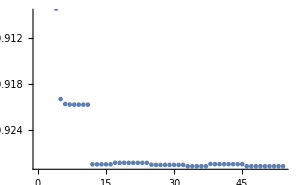

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:24:23 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:28:11, fev:759, <E>: -0.9298540776512021 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 25, 85}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 02:28:33, fev:1005, <E>: -0.9298540776512021 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 25, 89}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 02:29:03, fev:1325, <E>: -0.9298540776512021 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 25, 96}

dist 2.25 done with runtime 4.73356 min ϵ=0.00906831

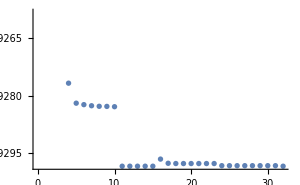

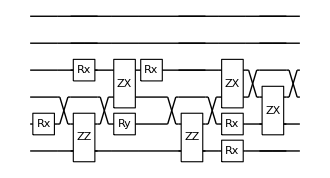

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:29:07 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:32:46, fev:720, <E>: -0.923245819574545 nansatz: 26 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 6, 76}

@cycle2:Thu 16 Feb 2023 02:34:02, fev:1281, <E>: -0.9297840244984912 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 18, 4, 25, 78}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 02:34:19, fev:1524, <E>: -0.9297840244984912 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 18, 4, 25, 82}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:34:41, fev:1836, <E>: -0.9297840244984912 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 18, 4, 25, 90}

dist 2.3 done with runtime 5.5733 min ϵ=0.00913836

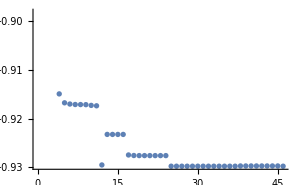

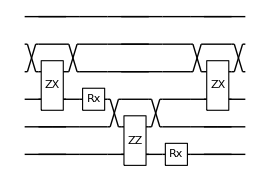

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:34:42 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:38:14, fev:857, <E>: -0.9303061005539717 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 13, 83}

@cycle2:Thu 16 Feb 2023 02:38:53, fev:1289, <E>: -0.9303299772417504 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 17, 88}

@cycle3:Thu 16 Feb 2023 02:39:30, fev:1706, <E>: -0.9305119363179255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 22, 95}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:39:57, fev:1954, <E>: -0.9305119363179255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 22, 97}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:40:27, fev:2251, <E>: -0.9305119363179255 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 22, 99}

dist 2.35 done with runtime 5.8882 min ϵ=0.00674302

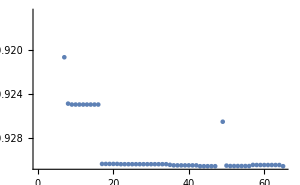

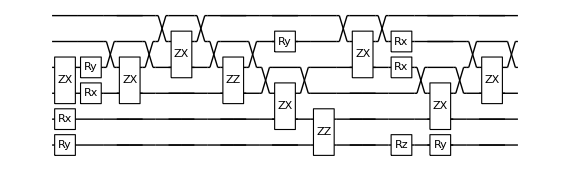

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:40:35 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:45:28, fev:1028, <E>: -0.9309023751971377 nansatz: 10 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 30, 84}

@cycle2:Thu 16 Feb 2023 02:45:57, fev:1427, <E>: -0.9309320165877467 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 32, 92}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 02:46:28, fev:1707, <E>: -0.9309320165877467 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 32, 96}

@cycle4:Thu 16 Feb 2023 02:47:07, fev:2192, <E>: -0.9309469411595137 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 36, 100}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:47:43, fev:2522, <E>: -0.9309469411595137 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 36, 104}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 02:48:26, fev:2921, <E>: -0.9309469411595137 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 36, 115}

dist 2.4 done with runtime 7.99267 min ϵ=0.00630801

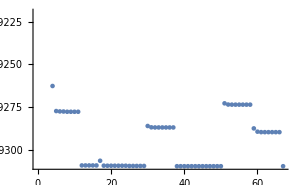

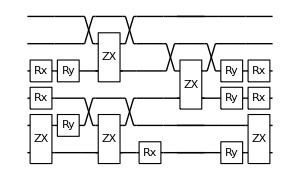

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:48:35 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:52:50, fev:897, <E>: -0.9289942863352136 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 13, 65}

@cycle2:Thu 16 Feb 2023 02:53:55, fev:1403, <E>: -0.9314186828086986 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 31, 71}

@cycle3:Thu 16 Feb 2023 02:54:06, fev:1667, <E>: -0.9314886033799458 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 33, 75}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:54:19, fev:1895, <E>: -0.9314886033799458 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 33, 78}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 02:54:39, fev:2209, <E>: -0.9314886033799458 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 17, 4, 33, 83}

dist 2.45 done with runtime 6.08364 min ϵ=0.00456632

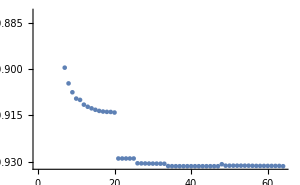

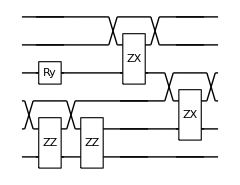

Compilation with automatically generated ansatz at Thu 16 Feb 2023 02:54:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 02:58:28, fev:720, <E>: -0.9275799521754197 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 19, 90}

@cycle2:Thu 16 Feb 2023 02:59:21, fev:1173, <E>: -0.9314196743784612 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 33, 98}

@cycle3:Thu 16 Feb 2023 02:59:39, fev:1498, <E>: -0.9314755580485014 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 34, 100}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 02:59:55, fev:1736, <E>: -0.9314755580485014 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 34, 105}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 03:00:20, fev:2060, <E>: -0.9314755580485014 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 34, 111}

dist 2.5 done with runtime 5.70795 min ϵ=0.00457936

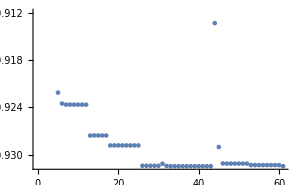

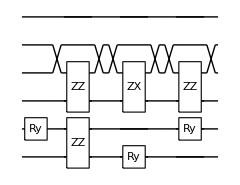

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:00:22 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:05:45, fev:974, <E>: -0.9319015564380232 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 13, 93}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:06:42, fev:1242, <E>: -0.9319015564380232 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 13, 98}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:07:56, fev:1567, <E>: -0.9319015564380232 nansatz: 28 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 13, 109}

dist 2.55 done with runtime 8.77221 min ϵ=0.00329444

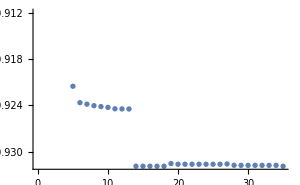

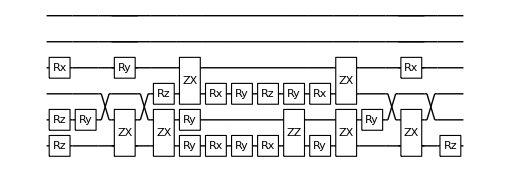

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:09:09 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:13:00, fev:713, <E>: -0.9317868859705042 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 18, 79}

@cycle2:Thu 16 Feb 2023 03:13:31, fev:1095, <E>: -0.9319294373446634 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 21, 83}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:13:51, fev:1331, <E>: -0.9319294373446634 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 21, 90}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 03:14:20, fev:1644, <E>: -0.9319294373446634 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 21, 98}

dist 2.6 done with runtime 5.30906 min ϵ=0.00326659

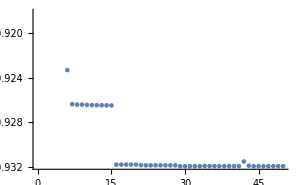

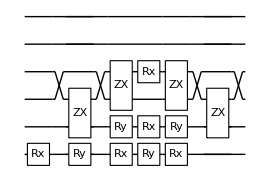

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:14:27 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:18:20, fev:1085, <E>: -0.9320078565552633 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 27, 102}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:18:42, fev:1319, <E>: -0.9320078565552633 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 27, 107}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:19:12, fev:1619, <E>: -0.9320078565552633 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 27, 113}

dist 2.65 done with runtime 4.80752 min ϵ=0.00257656

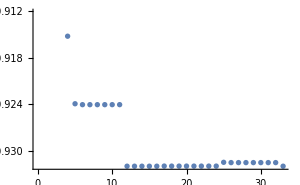

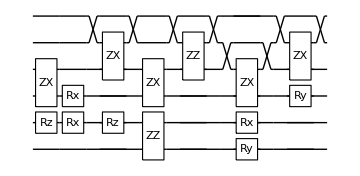

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:19:16 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:23:17, fev:811, <E>: -0.9322243478662735 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 8, 0, 24, 103}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:23:42, fev:1045, <E>: -0.9322243478662735 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 8, 0, 24, 107}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:24:20, fev:1376, <E>: -0.9322243478662735 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 8, 0, 24, 111}

dist 2.7 done with runtime 5.19627 min ϵ=0.00236007

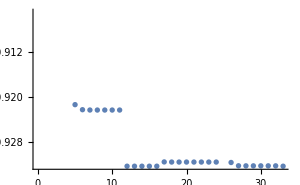

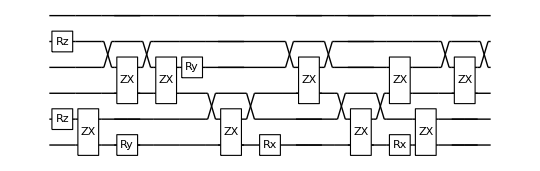

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:24:28 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:28:17, fev:731, <E>: -0.9325213232686269 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 13, 88}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:28:50, fev:981, <E>: -0.9325213232686269 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 13, 99}

@cycle3:Thu 16 Feb 2023 03:29:42, fev:1496, <E>: -0.932521324481792 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 18, 103}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 03:30:19, fev:1797, <E>: -0.932521324481792 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 18, 108}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 03:31:09, fev:2187, <E>: -0.932521324481792 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 18, 115}

dist 2.75 done with runtime 6.84358 min ϵ=0.00162977

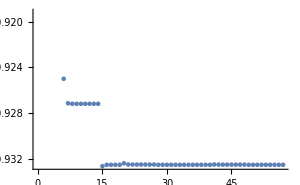

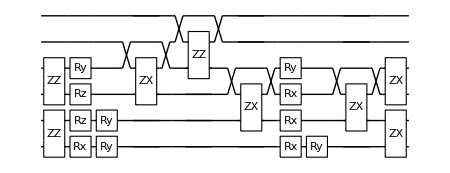

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:31:18 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:36:00, fev:1044, <E>: -0.9320468292523041 nansatz: 22 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 18, 81}

@cycle2:Thu 16 Feb 2023 03:36:52, fev:1491, <E>: -0.9325628898930087 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 18, 90}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:37:18, fev:1733, <E>: -0.9325628898930087 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 18, 97}

@cycle4:Thu 16 Feb 2023 03:38:12, fev:2230, <E>: -0.9325954520525527 nansatz: 15 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 21, 108}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 03:38:50, fev:2539, <E>: -0.9325954520525527 nansatz: 15 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 21, 109}

@cycle6:Thu 16 Feb 2023 03:39:58, fev:3137, <E>: -0.9326081196443134 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 25, 117}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 03:40:50, fev:3541, <E>: -0.9326081196443134 nansatz: 16 merged-smallθ-metric-bf-gmerged: {3, 18, 0, 25, 132}

@cycle8:Thu 16 Feb 2023 03:42:01, fev:4218, <E>: -0.932625375300348 nansatz: 19 merged-smallθ-metric-bf-gmerged: {3, 19, 0, 26, 139}

I'm slowing down @cycle 9

@cycle9:Thu 16 Feb 2023 03:43:01, fev:4694, <E>: -0.932625375300348 nansatz: 19 merged-smallθ-metric-bf-gmerged: {3, 19, 0, 26, 144}

I'm slowing down @cycle 10

@cycle10:Thu 16 Feb 2023 03:44:07, fev:5257, <E>: -0.932625375300348 nansatz: 19 merged-smallθ-metric-bf-gmerged: {3, 19, 0, 26, 150}

dist 2.8 done with runtime 12.9901 min ϵ=0.00152572

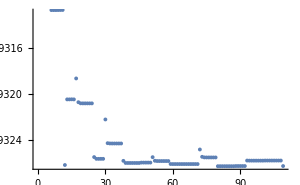

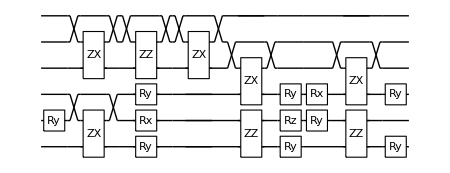

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:44:18 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:48:41, fev:1000, <E>: -0.9326567238778725 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 28, 80}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:49:11, fev:1259, <E>: -0.9326567238778725 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 28, 88}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:49:50, fev:1602, <E>: -0.9326567238778725 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 28, 92}

dist 2.85 done with runtime 5.63859 min ϵ=0.00118903

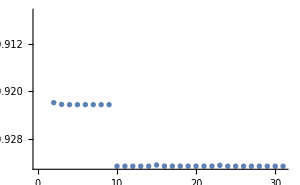

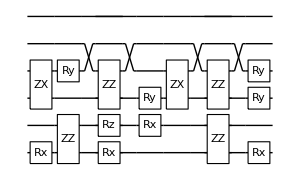

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:49:56 with grad NGAN

@cycle1:Thu 16 Feb 2023 03:54:36, fev:907, <E>: -0.9327908198573116 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 20, 81}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 03:55:04, fev:1146, <E>: -0.9327908198573116 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 20, 88}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 03:55:45, fev:1505, <E>: -0.9327908198573116 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 20, 90}

dist 2.9 done with runtime 5.925 min ϵ=0.00105493

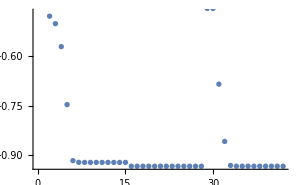

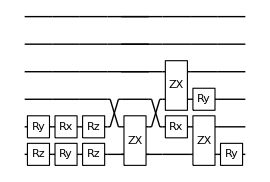

Compilation with automatically generated ansatz at Thu 16 Feb 2023 03:55:52 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:00:51, fev:1257, <E>: -0.9329186317638158 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 32, 72}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:01:14, fev:1501, <E>: -0.9329186317638158 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 32, 79}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:01:50, fev:1833, <E>: -0.9329186317638158 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 32, 91}

dist 2.95 done with runtime 6.10816 min ϵ=0.000713213

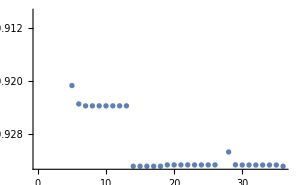

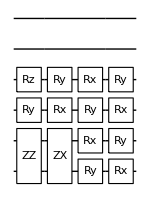

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:01:58 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:05:28, fev:761, <E>: -0.9327343219457488 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 4, 15, 80}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:05:54, fev:1033, <E>: -0.9327343219457488 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 4, 15, 84}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:06:25, fev:1347, <E>: -0.9327343219457488 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 4, 15, 88}

dist 3. done with runtime 4.52118 min ϵ=0.000897523

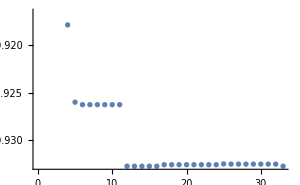

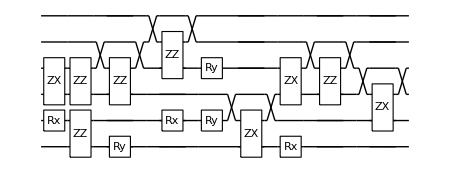

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:06:30 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:10:38, fev:708, <E>: -0.9328456272350063 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 9, 4, 29, 79}

@cycle2:Thu 16 Feb 2023 04:11:08, fev:1044, <E>: -0.9329132016839803 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 9, 4, 29, 84}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:11:38, fev:1298, <E>: -0.9329132016839803 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 9, 4, 29, 87}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 04:12:14, fev:1633, <E>: -0.9329132016839803 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 9, 4, 29, 91}

dist 3.05 done with runtime 5.84403 min ϵ=0.000569739

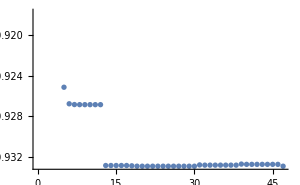

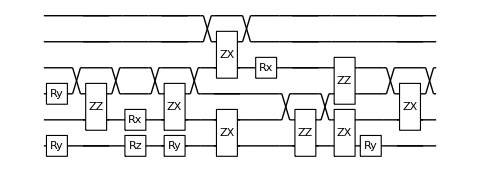

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:12:20 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:16:01, fev:807, <E>: -0.932850597482955 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 24, 72}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:16:22, fev:1061, <E>: -0.932850597482955 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 24, 79}

@cycle3:Thu 16 Feb 2023 04:16:56, fev:1520, <E>: -0.9328611264726421 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 26, 87}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 04:17:29, fev:1852, <E>: -0.9328611264726421 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 26, 96}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 04:18:10, fev:2254, <E>: -0.9328611264726421 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 5, 26, 105}

dist 3.1 done with runtime 5.89035 min ϵ=0.000621814

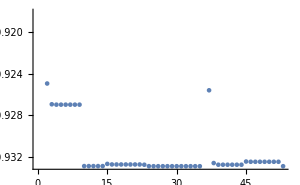

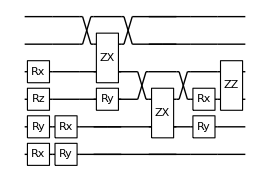

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:18:14 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:22:20, fev:768, <E>: -0.9324884081419625 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 18, 79}

@cycle2:Thu 16 Feb 2023 04:23:14, fev:1275, <E>: -0.9330632121792302 nansatz: 9 merged-smallθ-metric-bf-gmerged: {4, 10, 2, 31, 85}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:23:35, fev:1523, <E>: -0.9330632121792302 nansatz: 9 merged-smallθ-metric-bf-gmerged: {4, 10, 2, 31, 90}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 04:23:59, fev:1825, <E>: -0.9330632121792302 nansatz: 9 merged-smallθ-metric-bf-gmerged: {4, 10, 2, 31, 96}

dist 3.15 done with runtime 5.79533 min ϵ=0.000316765

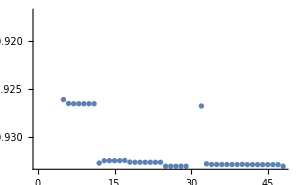

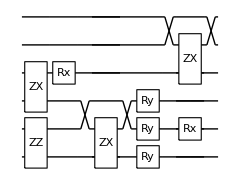

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:24:02 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:27:45, fev:670, <E>: -0.9330171354309741 nansatz: 5 merged-smallθ-metric-bf-gmerged: {5, 10, 2, 22, 75}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:28:03, fev:922, <E>: -0.9330171354309741 nansatz: 5 merged-smallθ-metric-bf-gmerged: {5, 10, 2, 22, 83}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:28:25, fev:1237, <E>: -0.9330171354309741 nansatz: 5 merged-smallθ-metric-bf-gmerged: {5, 10, 2, 22, 91}

dist 3.2 done with runtime 4.40259 min ϵ=0.000362842

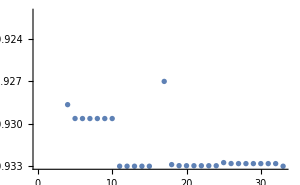

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:28:26 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:32:10, fev:810, <E>: -0.9327296771559604 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 18, 80}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:32:39, fev:1052, <E>: -0.9327296771559604 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 18, 90}

@cycle3:Thu 16 Feb 2023 04:33:33, fev:1577, <E>: -0.9327296781314083 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 23, 98}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 04:34:11, fev:1883, <E>: -0.9327296781314083 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 23, 105}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 04:35:01, fev:2262, <E>: -0.9327296781314083 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 23, 110}

dist 3.25 done with runtime 6.75234 min ϵ=0.000579594

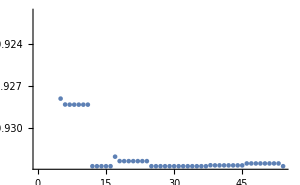

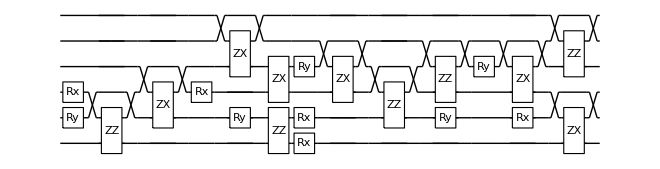

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:35:11 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:39:06, fev:735, <E>: -0.9326044277228535 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 17, 73}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:39:38, fev:970, <E>: -0.9326044277228535 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 17, 78}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:40:23, fev:1295, <E>: -0.9326044277228535 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 17, 88}

dist 3.3 done with runtime 5.81283 min ϵ=0.000356764

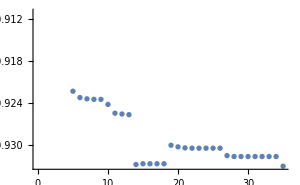

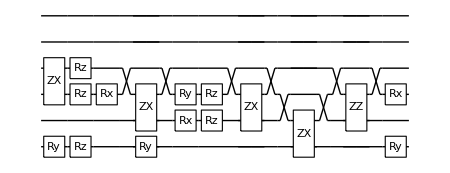

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:41:00 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:45:33, fev:1126, <E>: -0.9329391115918996 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 22, 100}

@cycle2:Thu 16 Feb 2023 04:46:19, fev:1576, <E>: -0.9326960353194095 nansatz: 17 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 26, 110}

@cycle3:Thu 16 Feb 2023 04:46:57, fev:2004, <E>: -0.9330113888256246 nansatz: 10 merged-smallθ-metric-bf-gmerged: {4, 11, 2, 32, 122}

@cycle4:Thu 16 Feb 2023 04:47:27, fev:2336, <E>: -0.9331002730963102 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 11, 2, 32, 128}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 04:47:55, fev:2585, <E>: -0.9331002730963102 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 11, 2, 32, 134}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 04:48:32, fev:2916, <E>: -0.9331002730963102 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 11, 2, 32, 137}

dist 3.35 done with runtime 7.66717 min ϵ=0.000160784

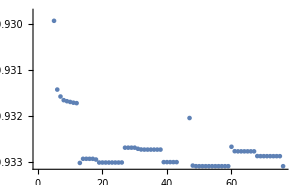

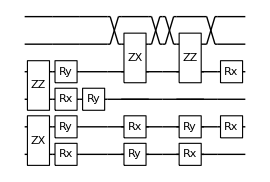

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:48:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:52:07, fev:738, <E>: -0.9331205797355522 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 78}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 04:52:21, fev:987, <E>: -0.9331205797355522 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 86}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 04:52:41, fev:1308, <E>: -0.9331205797355522 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 93}

dist 3.4 done with runtime 4.02256 min ϵ=0.000140478

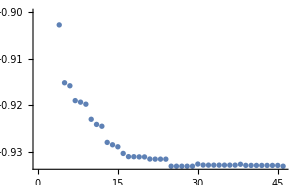

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 04:52:41 with grad NGAN

@cycle1:Thu 16 Feb 2023 04:57:01, fev:897, <E>: -0.9328693462604007 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 15, 84}

@cycle2:Thu 16 Feb 2023 04:58:31, fev:1464, <E>: -0.9329290657248687 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 17, 88}

@cycle3:Thu 16 Feb 2023 05:00:03, fev:2054, <E>: -0.9329426796919661 nansatz: 34 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 19, 97}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 05:00:45, fev:2282, <E>: -0.9329426796919661 nansatz: 34 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 19, 103}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 05:01:47, fev:2599, <E>: -0.9329426796919661 nansatz: 34 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 19, 113}

dist 3.45 done with runtime 9.59313 min ϵ=0.000285726

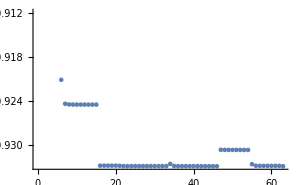

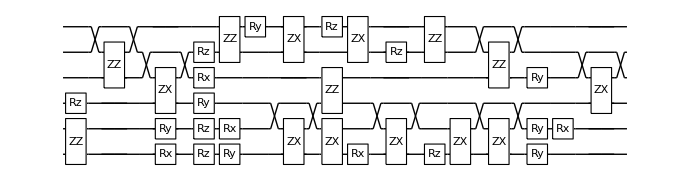

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:02:17 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:05:54, fev:668, <E>: -0.9331243078000578 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 9, 78}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:06:09, fev:912, <E>: -0.9331243078000578 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 9, 80}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:06:31, fev:1228, <E>: -0.9331243078000578 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 9, 86}

dist 3.5 done with runtime 4.25463 min ϵ=0.000104098

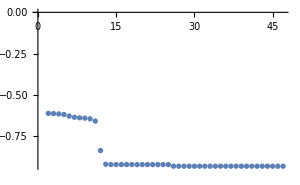

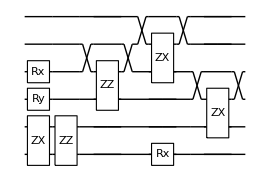

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:06:32 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:10:37, fev:884, <E>: -0.9331152802096578 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 17, 87}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:11:04, fev:1125, <E>: -0.9331152802096578 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 17, 94}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:11:48, fev:1459, <E>: -0.9331152802096578 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 17, 98}

dist 3.55 done with runtime 5.44085 min ϵ=0.0000911618

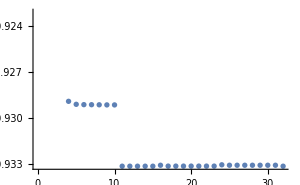

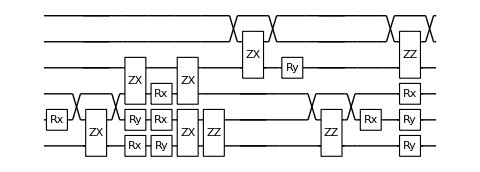

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:11:59 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:16:06, fev:800, <E>: -0.9330745638443202 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 9, 5, 15, 82}

@cycle2:Thu 16 Feb 2023 05:16:39, fev:1187, <E>: -0.9330976178451514 nansatz: 12 merged-smallθ-metric-bf-gmerged: {5, 9, 8, 18, 89}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:17:00, fev:1420, <E>: -0.9330976178451514 nansatz: 12 merged-smallθ-metric-bf-gmerged: {5, 9, 8, 18, 100}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 05:17:30, fev:1725, <E>: -0.9330976178451514 nansatz: 12 merged-smallθ-metric-bf-gmerged: {5, 9, 8, 18, 107}

dist 3.6 done with runtime 5.57796 min ϵ=0.000108824

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:17:34 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:21:15, fev:680, <E>: -0.9329733597671876 nansatz: 17 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 18, 79}

@cycle2:Thu 16 Feb 2023 05:22:07, fev:1123, <E>: -0.9330150877664782 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 22, 80}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:22:41, fev:1357, <E>: -0.9330150877664782 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 22, 89}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 05:23:34, fev:1692, <E>: -0.9330150877664782 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 22, 98}

dist 3.65 done with runtime 6.2471 min ϵ=0.000176676

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:23:49 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:28:40, fev:1226, <E>: -0.9330845570531658 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 17, 81}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:29:24, fev:1484, <E>: -0.9330845570531658 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 17, 86}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:30:23, fev:1808, <E>: -0.9330845570531658 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 17, 96}

dist 3.7 done with runtime 7.00382 min ϵ=0.000107207

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:30:49 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:34:24, fev:709, <E>: -0.9331036802383206 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 27, 0, 2, 89}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:34:56, fev:968, <E>: -0.9331036802383206 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 27, 0, 2, 94}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:35:35, fev:1273, <E>: -0.9331036802383206 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 27, 0, 2, 100}

dist 3.75 done with runtime 4.97803 min ϵ=0.0000783365

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:35:48 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:40:26, fev:878, <E>: -0.9258445643047845 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 84}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:41:49, fev:1154, <E>: -0.9258445643047845 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 88}

@cycle3:Thu 16 Feb 2023 05:43:48, fev:1695, <E>: -0.9331517472633241 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 9, 96}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 05:44:07, fev:2004, <E>: -0.9331517472633241 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 9, 107}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 05:44:29, fev:2381, <E>: -0.9331517472633241 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 9, 115}

dist 3.8 done with runtime 8.69479 min ϵ=0.0000302695

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:44:29 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:47:42, fev:725, <E>: -0.9330739518285052 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 7, 1, 19, 84}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 05:48:10, fev:992, <E>: -0.9330739518285052 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 7, 1, 19, 89}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:48:40, fev:1294, <E>: -0.9330739518285052 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 7, 1, 19, 96}

dist 3.85 done with runtime 4.27772 min ϵ=0.000101631

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:48:46 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:52:22, fev:787, <E>: -0.925874831460568 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 27, 74}

@cycle2:Thu 16 Feb 2023 05:52:51, fev:1193, <E>: -0.933112540409218 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 81}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 05:53:03, fev:1425, <E>: -0.933112540409218 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 87}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 05:53:22, fev:1746, <E>: -0.933112540409218 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 34, 90}

dist 3.9 done with runtime 4.5956 min ϵ=0.0000630427

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 05:53:22 with grad NGAN

@cycle1:Thu 16 Feb 2023 05:57:43, fev:936, <E>: -0.9326854869949329 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 13, 3, 11, 79}

@cycle2:Thu 16 Feb 2023 05:58:58, fev:1565, <E>: -0.932992242450595 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 18, 3, 18, 82}

@cycle3:Thu 16 Feb 2023 05:59:44, fev:1965, <E>: -0.9329923071798679 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 18, 3, 19, 93}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 06:00:18, fev:2208, <E>: -0.9329923071798679 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 18, 3, 19, 101}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 06:00:59, fev:2517, <E>: -0.9329923071798679 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 18, 3, 19, 108}

dist 3.95 done with runtime 7.7429 min ϵ=0.000179055

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:01:07 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:04:32, fev:697, <E>: -0.9331441458777454 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 21, 108}

@cycle2:Thu 16 Feb 2023 06:04:49, fev:999, <E>: -0.9331452823074683 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 24, 120}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:05:05, fev:1240, <E>: -0.9331452823074683 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 24, 134}

@cycle4:Thu 16 Feb 2023 06:05:28, fev:1622, <E>: -0.9331452824686571 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 27, 146}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 06:05:49, fev:1936, <E>: -0.9331452824686571 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 27, 159}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 06:06:16, fev:2343, <E>: -0.9331452824686571 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 4, 3, 27, 162}

dist 4. done with runtime 5.17583 min ϵ=0.0000260794

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:06:17 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:10:56, fev:952, <E>: -0.9330967430405245 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 12, 69}

@cycle2:Thu 16 Feb 2023 06:12:24, fev:1515, <E>: -0.9331109750797286 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 16, 76}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:13:14, fev:1784, <E>: -0.9331109750797286 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 16, 88}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 06:14:18, fev:2121, <E>: -0.9331109750797286 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 16, 96}

dist 4.05 done with runtime 8.47204 min ϵ=0.0000576336

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:14:46 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:18:24, fev:756, <E>: -0.9326466454627346 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 27, 71}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:18:48, fev:984, <E>: -0.9326466454627346 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 27, 82}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:19:20, fev:1282, <E>: -0.9326466454627346 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 27, 92}

dist 4.1 done with runtime 4.74936 min ϵ=0.000394508

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:19:31 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:23:12, fev:676, <E>: -0.9330530893173681 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 6, 108}

@cycle2:Thu 16 Feb 2023 06:23:34, fev:1004, <E>: -0.9331493136796215 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 11, 113}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:23:49, fev:1233, <E>: -0.9331493136796215 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 11, 122}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 06:24:12, fev:1538, <E>: -0.9331493136796215 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 11, 127}

dist 4.15 done with runtime 4.71918 min ϵ=0.0000175102

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:24:14 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:28:12, fev:796, <E>: -0.9330654670625194 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 14, 87}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:28:47, fev:1039, <E>: -0.9330654670625194 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 14, 93}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:29:35, fev:1342, <E>: -0.9330654670625194 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 14, 106}

dist 4.2 done with runtime 5.73415 min ϵ=0.0000778037

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:29:58 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:35:15, fev:1251, <E>: -0.9331163251114949 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 1, 2, 34, 95}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:35:37, fev:1502, <E>: -0.9331163251114949 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 1, 2, 34, 100}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:36:06, fev:1837, <E>: -0.9331163251114949 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 1, 2, 34, 106}

dist 4.25 done with runtime 6.18425 min ϵ=0.0000493488

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:36:09 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:41:34, fev:1095, <E>: -0.9330894012981937 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 10, 1, 32, 100}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:41:58, fev:1341, <E>: -0.9330894012981937 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 10, 1, 32, 103}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:42:35, fev:1669, <E>: -0.9330894012981937 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 10, 1, 32, 110}

dist 4.3 done with runtime 6.52019 min ϵ=0.0000762726

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:42:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:46:44, fev:910, <E>: -0.9329019758292926 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 12, 83}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:47:12, fev:1142, <E>: -0.9329019758292926 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 12, 95}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 06:47:49, fev:1460, <E>: -0.9329019758292926 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 12, 100}

dist 4.35 done with runtime 5.30388 min ϵ=0.000262962

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:47:59 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:51:25, fev:835, <E>: -0.933124010689159 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 17, 74}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 06:51:40, fev:1067, <E>: -0.933124010689159 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 17, 83}

@cycle3:Thu 16 Feb 2023 06:52:07, fev:1497, <E>: -0.9331586125786928 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 86}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 06:52:31, fev:1800, <E>: -0.9331586125786928 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 92}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 06:52:59, fev:2181, <E>: -0.9331586125786928 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 100}

dist 4.4 done with runtime 5.08523 min ϵ=6.32535×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 06:53:04 with grad NGAN

@cycle1:Thu 16 Feb 2023 06:56:53, fev:719, <E>: -0.93314649856575 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 11, 101}

@cycle2:Thu 16 Feb 2023 06:57:24, fev:1097, <E>: -0.9331546511003922 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 13, 108}

@cycle3:Thu 16 Feb 2023 06:57:58, fev:1466, <E>: -0.9331546511006666 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 15, 121}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 06:58:23, fev:1712, <E>: -0.9331546511006666 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 15, 125}

@cycle5:Thu 16 Feb 2023 06:59:12, fev:2209, <E>: -0.9331570638556941 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 18, 132}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 06:59:44, fev:2516, <E>: -0.9331570638556941 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 18, 144}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 07:00:26, fev:2901, <E>: -0.9331570638556941 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 17, 0, 18, 155}

dist 4.45 done with runtime 7.50227 min ϵ=7.40623×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:00:34 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:04:27, fev:777, <E>: -0.9331544981341142 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 23, 82}

@cycle2:Thu 16 Feb 2023 07:04:54, fev:1149, <E>: -0.9331545141028879 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 28, 94}

@cycle3:Thu 16 Feb 2023 07:05:28, fev:1512, <E>: -0.9331581496967136 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 28, 99}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:05:53, fev:1759, <E>: -0.9331581496967136 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 28, 107}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 07:06:31, fev:2103, <E>: -0.9331581496967136 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 28, 109}

dist 4.5 done with runtime 6.10083 min ϵ=6.32039×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:06:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:10:05, fev:627, <E>: -0.9261742010131009 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 7, 91}

@cycle2:Thu 16 Feb 2023 07:10:33, fev:976, <E>: -0.9304886971380528 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 17, 3, 9, 96}

@cycle3:Thu 16 Feb 2023 07:10:50, fev:1298, <E>: -0.9315556096784413 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 19, 3, 10, 101}

@cycle4:Thu 16 Feb 2023 07:11:11, fev:1646, <E>: -0.932855225160398 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 21, 3, 13, 108}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 07:11:30, fev:1880, <E>: -0.932855225160398 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 21, 3, 13, 113}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 07:11:55, fev:2205, <E>: -0.932855225160398 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 21, 3, 13, 119}

dist 4.55 done with runtime 5.27324 min ϵ=0.00030895

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:11:57 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:15:44, fev:714, <E>: -0.932903077518562 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 5, 87}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 07:16:16, fev:988, <E>: -0.932903077518562 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 5, 91}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 07:16:53, fev:1318, <E>: -0.932903077518562 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 5, 98}

dist 4.6 done with runtime 5.07673 min ϵ=0.000261097

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:17:01 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:21:38, fev:800, <E>: -0.9294809359856818 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 13, 0, 14, 82}

@cycle2:Thu 16 Feb 2023 07:22:38, fev:1336, <E>: -0.9329111590331015 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 18, 1, 25, 92}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 07:22:56, fev:1587, <E>: -0.9329111590331015 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 18, 1, 25, 100}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:23:23, fev:1905, <E>: -0.9329111590331015 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 18, 1, 25, 104}

dist 4.65 done with runtime 6.37896 min ϵ=0.000252831

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:23:24 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:27:23, fev:784, <E>: -0.9331122576465173 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 8, 3, 19, 83}

@cycle2:Thu 16 Feb 2023 07:27:45, fev:1149, <E>: -0.9331523221537252 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 9, 3, 22, 89}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 07:28:02, fev:1394, <E>: -0.9331523221537252 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 9, 3, 22, 98}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:28:20, fev:1686, <E>: -0.9331523221537252 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 9, 3, 22, 107}

dist 4.7 done with runtime 4.93817 min ϵ=0.000011668

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:28:21 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:32:46, fev:781, <E>: -0.9330431381720641 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 2, 81}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 07:33:39, fev:1023, <E>: -0.9330431381720641 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 2, 87}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 07:34:46, fev:1329, <E>: -0.9330431381720641 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 2, 93}

dist 4.75 done with runtime 7.11004 min ϵ=0.000120737

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:35:27 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:39:03, fev:780, <E>: -0.9216248744120645 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 14, 85}

@cycle2:Thu 16 Feb 2023 07:39:41, fev:1211, <E>: -0.9268373219314098 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 14, 92}

@cycle3:Thu 16 Feb 2023 07:40:06, fev:1517, <E>: -0.9330361765704458 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 27, 1, 19, 96}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:40:22, fev:1748, <E>: -0.9330361765704458 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 27, 1, 19, 98}

@cycle5:Thu 16 Feb 2023 07:40:39, fev:2086, <E>: -0.933128974549187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 27, 1, 24, 101}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 07:41:00, fev:2411, <E>: -0.933128974549187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 27, 1, 24, 111}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 07:41:26, fev:2821, <E>: -0.933128974549187 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 27, 1, 24, 114}

dist 4.8 done with runtime 5.97846 min ϵ=0.0000349009

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:41:26 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:45:42, fev:843, <E>: -0.9328363601421941 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 10, 74}

@cycle2:Thu 16 Feb 2023 07:46:34, fev:1406, <E>: -0.9331547090768305 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 19, 1, 28, 81}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 07:46:49, fev:1654, <E>: -0.9331547090768305 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 19, 1, 28, 84}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:47:07, fev:1958, <E>: -0.9331547090768305 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 19, 1, 28, 91}

dist 4.85 done with runtime 5.70708 min ϵ=9.09583×10^-6

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:47:09 with grad NGAN

@cycle1:Thu 16 Feb 2023 07:52:02, fev:843, <E>: -0.9315708972684685 nansatz: 45 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 89}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 07:53:32, fev:1100, <E>: -0.9315708972684685 nansatz: 45 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 95}

@cycle3:Thu 16 Feb 2023 07:56:02, fev:1728, <E>: -0.9327102659906408 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 26, 0, 11, 105}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 07:56:32, fev:2061, <E>: -0.9327102659906408 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 26, 0, 11, 110}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 07:57:10, fev:2455, <E>: -0.9327102659906408 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 26, 0, 11, 116}

dist 4.9 done with runtime 10.0923 min ϵ=0.000453539

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 07:57:14 with grad NGAN

@cycle1:Thu 16 Feb 2023 08:01:47, fev:954, <E>: -0.9327256817414558 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 22, 76}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 08:02:29, fev:1197, <E>: -0.9327256817414558 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 22, 79}

@cycle3:Thu 16 Feb 2023 08:03:56, fev:1806, <E>: -0.9329537160640424 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 26, 83}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 08:04:53, fev:2122, <E>: -0.9329537160640424 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 26, 87}

I'm slowing down @cycle 5

@cycle5:Thu 16 Feb 2023 08:06:04, fev:2519, <E>: -0.9329537160640424 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 26, 91}

dist 4.95 done with runtime 9.20932 min ϵ=0.000210046

-Graphics-

-Graphics-

Compilation with automatically generated ansatz at Thu 16 Feb 2023 08:06:27 with grad NGAN

@cycle1:Thu 16 Feb 2023 08:10:12, fev:750, <E>: -0.9324346806823666 nansatz: 22 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 7, 99}

@cycle2:Thu 16 Feb 2023 08:11:13, fev:1170, <E>: -0.9328102951715196 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 7, 0, 9, 109}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 08:11:49, fev:1422, <E>: -0.9328102951715196 nansatz: 15 merged-smallθ-metric-bf-gmerged: {4, 7, 0, 9, 112}

@cycle4:Thu 16 Feb 2023 08:12:57, fev:1930, <E>: -0.9328283879671888 nansatz: 16 merged-smallθ-metric-bf-gmerged: {4, 8, 0, 10, 118}

@cycle5:Thu 16 Feb 2023 08:14:02, fev:2418, <E>: -0.9329034695251364 nansatz: 16 merged-smallθ-metric-bf-gmerged: {4, 11, 1, 12, 128}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 08:14:50, fev:2729, <E>: -0.9329034695251364 nansatz: 16 merged-smallθ-metric-bf-gmerged: {4, 11, 1, 12, 137}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 08:15:50, fev:3113, <E>: -0.9329034695251364 nansatz: 16 merged-smallθ-metric-bf-gmerged: {4, 11, 1, 12, 144}

dist 5. done with runtime 9.63211 min ϵ=0.000260292

-Graphics-

-Graphics-

```mathematica
Table[
fname=ToString@StringForm["H3_hamiltonians/H3_``.txt",NumberForm[dist,{2,2}]];
{ham,nterms,nq}=FormatHamiltonian[fname];
dev=SuperconductingHub[];
conf=DefaultConfig[dev,ham];
res=VQEonVQD[conf];
{runtime,cost,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
AppendTo[H3onSQC,
<|
"description"->dist,
"hamiltonian"->ham,
"runtime"->runtime,
"ansatz"->ansatz,
"θvars"->θvars,
"groundstate"->conf["groundstate"],
"cost"->cost,
"fev"->fev
|>
];
DumpSave["H3onSQC.mx",H3onSQC];
Print["dist ",dist," done with runtime ",runtime, " ϵ=",Last@Elist-conf["groundstate"]];
Print[ListPlot[Elist,ImageSize->300]];
Print[DrawCircuit[ansatz,6]];
,{dist,distances}];
```

### Summary